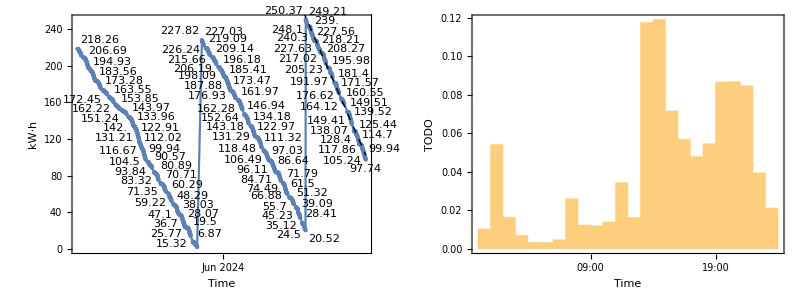
-Graphics-

Average: | -682.793 W, -16.387kWh/d
Linear Model: | FittedModel[321605.-0.00018702 ts]
Time to Zero: | Sat 29 Jun 2024 11:06:04GMT+8 in: 4.27419 days

```mathematica
Clear["`*"];
kwhLabelText = "kW"<>FromCharacterCode[8901]<>"h";
jsonRepr = Developer`ReadRawJSONString;
realRepr = Internal`StringToMReal;
imported = Import["~/electricity/electricity.jsonl", "Text"];
parseLine[line_] :=Module[{json},
        json = jsonRepr[line];
        {FromUnixTime[json["at"]], realRepr @ json["data"]["balance"]}
    ];
selectLastDecreasingIndex[data_]:=Module[{diff,positions},
diff=Differences@data;
positions=Flatten@Position[diff,x_/;x>0];
If[positions=={},1,Last@positions+1]
];
data=parseLine /@ StringSplit[imported, "\n"];
outputText = DateString @ #[[1]] <> "\t" <> ToString @ #[[2]] <> "\n"& /@data//StringJoin;
Export["~/electricity/electricity.txt", outputText];
(*data=Select[data,Now-Quantity[24*5,"Hours"]<#[[1]]<Now&];*)
dataDedupe =Module[{test},
        test[a_, b_] := a[[2]] == b[[2]];
        DeleteAdjacentDuplicates[data, test]
    ];
dataDedupe=Select[dataDedupe,#[[2]]!=0.0&];
lastDecreasingData=dataDedupe[[selectLastDecreasingIndex[#[[2]]&/@dataDedupe];;]];

lm = LinearModelFit[{UnixTime @ #[[1]], #[[2]]}& /@ lastDecreasingData, ts, ts];
lmNormal = Normal @ lm;
lmTime[obj_] := lmNormal /. ts -> UnixTime @ obj;

toZeroAt=FromUnixTime[ts /. Solve[lmNormal == 0, ts][[1, 1]]];

dateListPlot :=
    Module[{start, end, range, ticks, bottomMsg},
        start = dataDedupe[[1, 1]];
        end = dataDedupe[[-1, 1]];
        range = end - start;
        ticks =Module[{fragments = 7, increment},
                increment = range / fragments;
                start + increment (# - 1)& /@ Table[n, {n, fragments+1}]
            ];
        DateListPlot[Tooltip[Labeled[#, #[[2]]], #]& /@ dataDedupe, # [[2]]&,
 Joined -> True, 
 PlotStyle -> {PointSize[Medium]}, 
 Mesh -> Full,
 ImageSize->Large,
 FrameLabel -> {{kwhLabelText, None}, {"Time", None  }},
 DateTicksFormat -> {"MonthNameShort", " ", "Day", "\n", "Hour24",":", "Minute"},
 FrameTicks -> {{Automatic, None}, {ticks, None}},
 GridLines-> {Automatic, Automatic}, 
 Epilog -> {Dashed, Line[{{start, lmTime @ start}, {end, lmTime @ end}}]}]
    ];

histogram := Module[{diff, diffData, histogramData},
        diff = {#[[1]], -#[[2]]}& /@ Differences[lastDecreasingData];
        diffData = Transpose[{#[[1]]& /@ lastDecreasingData[[1 ;; -2]], diff}];
        histogramData = {#[[1]], #[[2, 2]]}& /@ Select[diffData, #[[2,1]] < Quantity[1.2, "Hours"]&];
        DateHistogram[
WeightedData[#[[1]]& /@ histogramData, #[[2]]& /@ histogramData],
 Quantity[60, "Minutes"],
 "Probability",
DateReduction -> "Day", 
ImageSize -> Large,
 Frame -> True,
 FrameLabel -> {{Style["TODO",Italic], None}, {"Time", None}}
]
    ];

bottomMsg = Grid[{
{"Average:", Row[{
UnitConvert[((lastDecreasingData[[-1, 2]] - lastDecreasingData[[1, 2]]) Quantity["Kilowatts"] Quantity["Hours"])/(lastDecreasingData[[-1,1]] - lastDecreasingData[[1, 1]]),"Watts"],
", " <> ToString @ ((lastDecreasingData⟦-1,2⟧-lastDecreasingData⟦1,2⟧)/((lastDecreasingData⟦-1,1⟧-lastDecreasingData⟦1,1⟧)/Quantity["Days"]) ) <> "kWh/d"
}]}, 
{"Linear Model:", AccountingForm@lm},
 {"Time to Zero:",Row[{toZeroAt," in: ",toZeroAt-Now}]}
},
 Frame -> All
    ];

result = Column[{
Grid[{
{dateListPlot, histogram}
},
Alignment -> {Center,Center}
],
 Spacer[30], 
bottomMsg
},
 Alignment -> Center
];

Export["electricity.svg", result];
Export["exports.json",{
"electricity"->Last[lastDecreasingData][[2]],
"toZeroAt"->UnixTime[toZeroAt]
}];

result
```